```mathematica
Clear[η]
```

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=10;xinitial={0,0.5};yinitial={-L0,0};
equs={m x''[t]==-k(1-L0/(√(x[t]^2+y[t]^2)))x[t]-η x'[t],m y''[t]==k(-1+L0/(√(x[t]^2+y[t]^2)))y[t]-m g-η y'[t],x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
Do[s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->10^6];
{x,y}={x,y}/.s[[1]];
p=ParametricPlot[{x[t],y[t]},{t,0,tm},PlotRange->{{-0.5,0.5},{-5,0.5}},AspectRatio->0.5,Epilog->Text["η="<>ToString[η],{0.3,-1}]];Print[p];Clear[x,y],{η,0.01,0.2,0.01}]
Clear[g,k,m,L0,tm,equs,s,x,y,η]
```

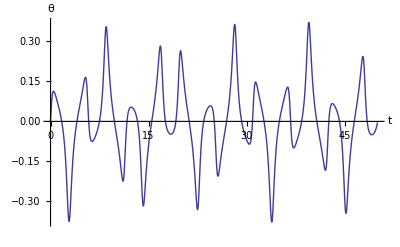

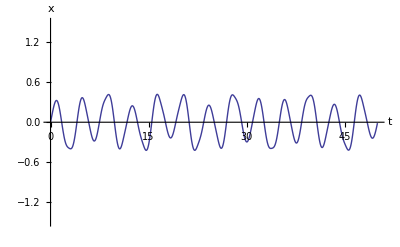

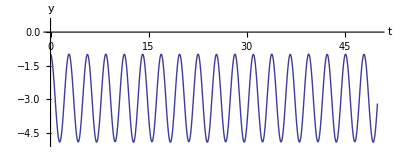

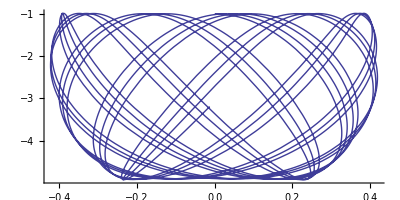

```mathematica
g=49/5;k=1/10;m=1/50;L0=1;tm=50;xinitial={0,1/2};yinitial={-L0,0};
equs={m x''[t]==-k(1-L0/(√(x[t]^2+y[t]^2)))x[t],m y''[t]==k(-1+L0/(√(x[t]^2+y[t]^2)))y[t]-m g,x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->20000];
{x,y}={x,y}/.s[[1]];
θ[t_]:=Arg[-y[t]+x[t]ⅈ];
Plot[θ[t],{t,0,tm},PlotRange->All,AxesLabel->{"t","θ"}]
Plot[x[t],{t,0,tm},PlotRange->{-1.5,1.5},AxesLabel->{"t","x"}]
Plot[y[t],{t,0,tm},PlotRange->{-5,0.5},AxesLabel->{"t","y"},AspectRatio->0.4]
ParametricPlot[{x[t],y[t]},{t,0,tm},AspectRatio->0.5]
```

```mathematica
Clear[g,k,m,L0,tm,equs,s,x,y,η]
```

```mathematica
Energy[t_]:=1/2 m(x'[t]^2+y'[t]^2)+m g y[t]+1/2 k (√(x[t]^2+y[t]^2)-L0)^2;
Plot[Energy[t],{t,0,tm}]
```